{Binding Energy cs, bs, cc, bc, bb}

-0.0246512

-0.0319728

-0.0771792

-0.100745

-0.128011

{Ξc 1/2+ 2.469}

{2.43596,4.88755,{3.07881,2.95407,2.48126,2.04279}}

{0.626331,0.319576}

{{0.187168,0.187168},{0.177284,0.177284}}

{Ξc' 1/2+ 2.579}

{2.54418,4.87823,{3.07869,2.95374,2.48071,2.04279}}

{0.62515,0.318941}

{{0.205951,-0.451946},{0.195075,-0.428079}}

{Ξc^* 3/2+ 2.646}

{2.63643,5.05567,{3.08088,2.95984,2.49106,2.04279}}

{0.647653,0.331007}

{{0.607687,-0.415055},{0.575595,-0.393137}}

{Ωc 1/2+ 2.695}

{2.67989,4.93207,{3.07937,2.95563,2.48388,2.04279}}

{0.280115}

{{-0.40578},{-0.384351}}

{Ωc^* 3/2+ 2.766}

{2.76395,5.09816,{3.08138,2.96124,2.4935,2.04279}}

{0.288747}

{{-0.339315},{-0.321396}}

{Ds 0- 1.968}

{1.9609,3.77264,{3.06053,2.90466,2.40965,2.04279}}

{0.460299,0.460299}

{Ds^* 1- 2.112}

{2.112,4.17192,{3.06818,2.92497,2.4367,2.04279}}

{0.505227,0.505227}

{{0.409371,-0.409371},{0.387753,-0.387753}}

{Ξb 1/2+ 5.794}

{5.80488,4.63633,{3.07544,2.94475,2.46616,2.04279}}

{0.29526,0.598098}

{{-0.0323638,-0.0323638},{-0.0306547,-0.0306547}}

{Ξb' 1/2+ 5.935}

{5.95569,4.70604,{3.07641,2.94743,2.47041,2.04279}}

{0.300259,0.606814}

{{0.268114,-0.366561},{0.253955,-0.347203}}

{Ξb^* 3/2+ 5.954}

{5.9906,4.78947,{3.07754,2.95053,2.47544,2.04279}}

{0.306254,0.617239}

{{0.361575,-0.607314},{0.342481,-0.575242}}

{Ωb 1/2+ 6.046}

{6.07969,4.76783,{3.07725,2.94974,2.47414,2.04279}}

{0.59529}

{{-0.324032},{-0.30692}}

{Ωb^* 3/2+}

{6.11176,4.84453,{3.07826,2.95253,2.47872,2.04279}}

{0.604289}

{{-0.540609},{-0.51206}}

{Bs 0- 5.367}

{5.34636,3.35218,{3.05055,2.87898,2.37928,2.04279}}

{0.157975,0.157975}

{Bs^* 1- 5.415}

{5.415,3.61935,{3.05715,2.89587,2.39881,2.04279}}

{0.169315,0.169315}

{{0.380142,-0.380142},{0.360067,-0.360067}}

{ηc 0- 2.984}

{3.00164,3.15224,{3.04491,2.86484,2.36412,2.04279}}

{0.}

{Jψ 1- 3.097}

{3.097,3.54106,{3.05532,2.89114,2.39317,2.04279}}

{0.}

{{0.},{0.}}

{Bc 0- 6.275}

{6.275,2.53226,{3.02197,2.81036,2.31386,2.04279}}

{0.294459,0.294459}

{Bc^* 1-}

{6.33335,2.81449,{3.03362,2.83743,2.33737,2.04279}}

{0.324436,0.324436}

{{0.197971,-0.197971},{0.187517,-0.187517}}

{ηb 0- 9.399}

{9.39655,1.59205,{2.95594,2.6778,2.22705,2.04279}}

{0.}

{Υ 1- 9.460}

{9.46,1.79829,{2.97584,2.71427,2.2473,2.04279}}

{0.}

{{0.},{0.}}

{Ξcc 1/2+ 3.621}

{3.60392,4.42057,{3.07225,2.93601,2.45273,2.04279}}

{0.778419,0.448868}

{{0.0470245,0.345112},{0.0445412,0.326887}}

{Ξcc^* 3/2+ 1.533}

{3.71416,4.63766,{3.07546,2.9448,2.46624,2.04279}}

{0.815011,0.468068}

{{0.996903,0.0587224},{0.944257,0.0556213}}

{Ξbb 1/2+}

{10.3106,3.70724,{3.05912,2.90099,2.40505,2.04279}}

{0.287456,0.449248}

{{-0.209554,0.0404325},{-0.198487,0.0382973}}

{Ξbb^* 3/2+}

{10.3595,3.86546,{3.06244,2.9097,2.41609,2.04279}}

{0.300223,0.468103}

{{0.456882,-0.325084},{0.432755,-0.307916}}

{Mass Spectrum}

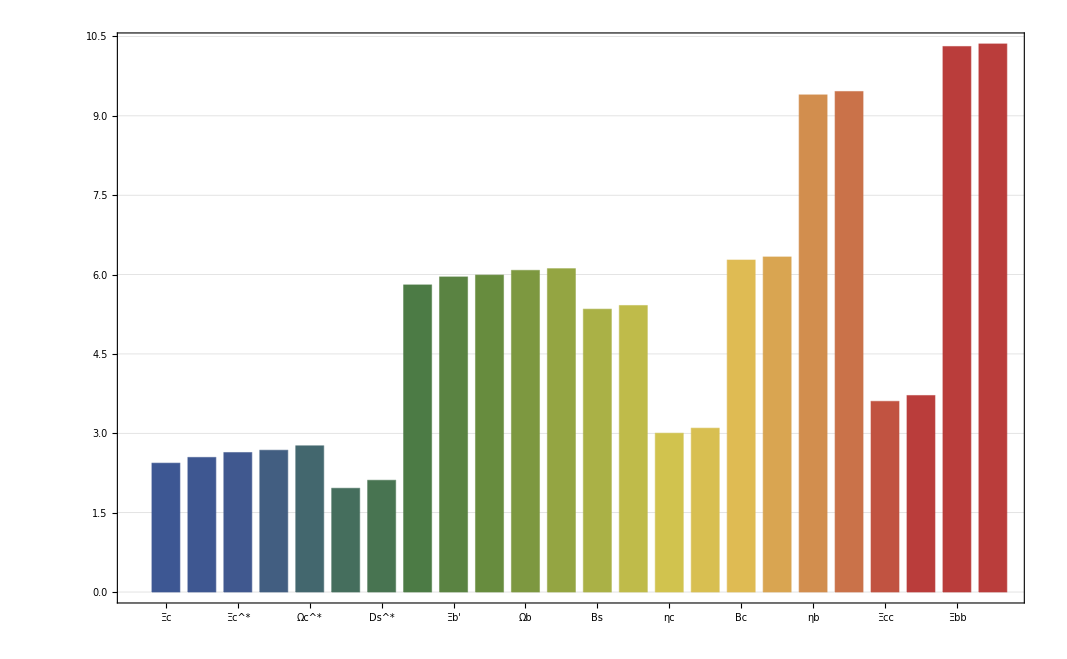

{My Error}

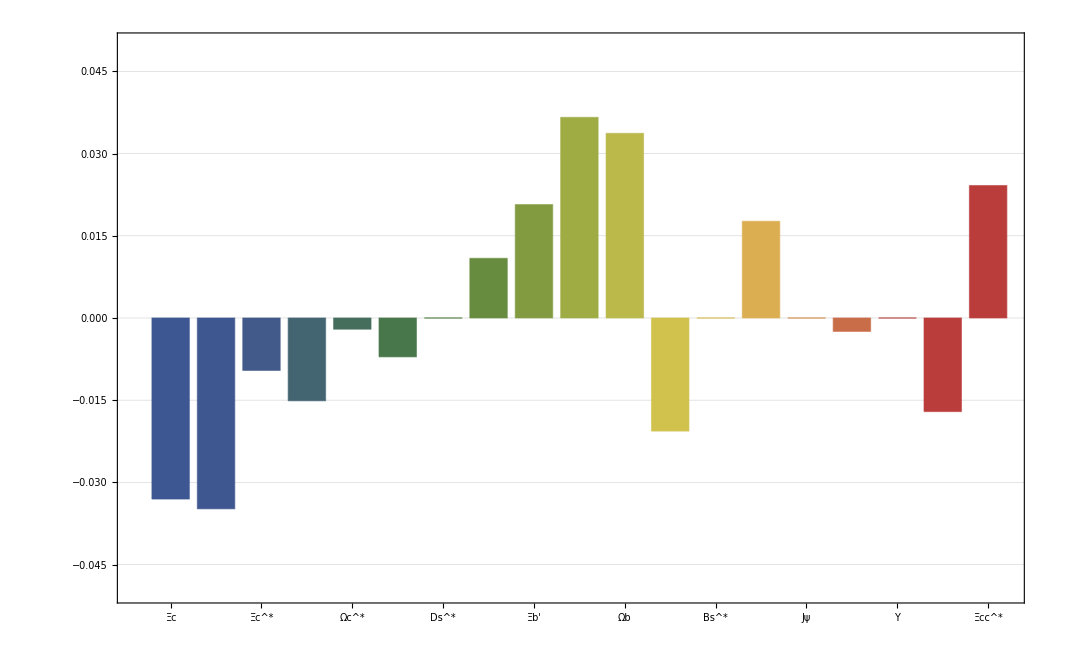

{Charge Radius}

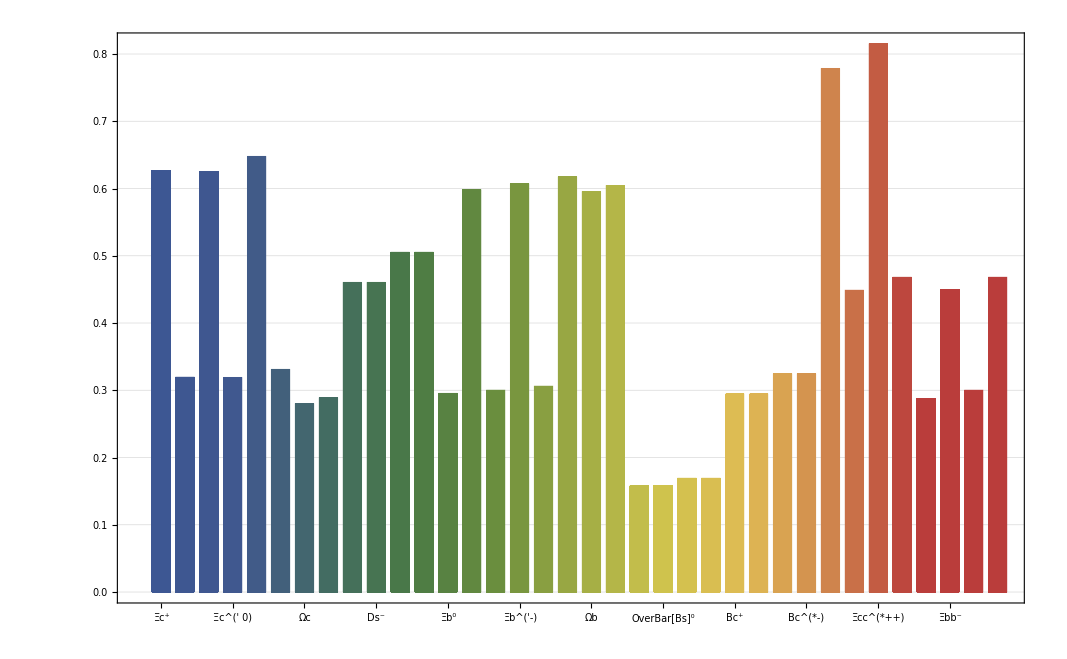

{Magnetic Moment}

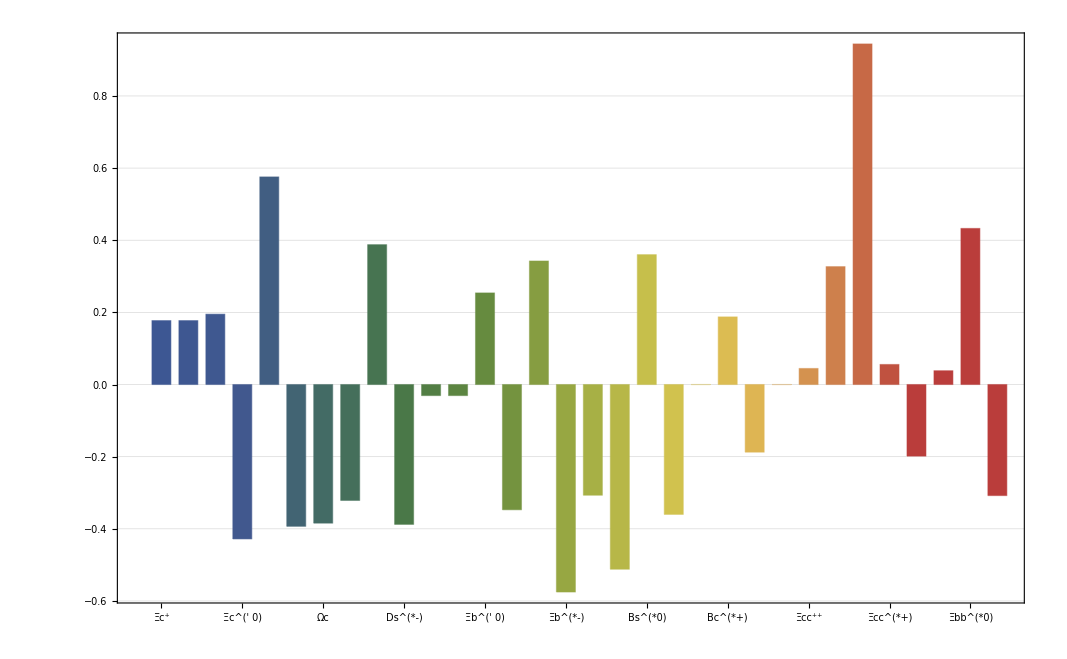

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.275)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ξc 1/2+ 2.469"}
Ξc=Hadron[{0,1,1,1},{{0,0,0,0},{0,0,0,0},{0,0,0,8},{0,0,0,0}},Bcs]
rΞcp=ChargeRadius[{0,1,1,1,0},{0,0,0,0,0},Ξc];
rΞc0=ChargeRadius[{0,1,1,0,1},{0,0,0,0,0},Ξc];
μΞcp=MagneticMoment[{0,1,0,0,0},{0,0,0,0,0},Ξc];
μΞc0=MagneticMoment[{0,1,0,0,0},{0,0,0,0,0},Ξc];
{rΞcp,rΞc0}
{{μΞcp,μΞc0},{μΞcp/μNp,μΞc0/μNp}}

{"Ξc' 1/2+ 2.579"}
ΞcPrime=Hadron[{0,1,1,1},{{0,0,0,0},{0,0,16/3,16/3},{0,0,0,-8/3},{0,0,0,0}},Bcs]
rΞcpPrime=ChargeRadius[{0,1,1,1,0},{0,0,0,0,0},ΞcPrime];
rΞc0Prime=ChargeRadius[{0,1,1,0,1},{0,0,0,0,0},ΞcPrime];
μΞcpPrime=MagneticMoment[{0,-1/3,2/3,2/3,0},{0,0,0,0,0},ΞcPrime];
μΞc0Prime=MagneticMoment[{0,-1/3,2/3,0,2/3},{0,0,0,0,0},ΞcPrime];
{rΞcpPrime,rΞc0Prime}
{{μΞcpPrime,μΞc0Prime},{μΞcpPrime/μNp,μΞc0Prime/μNp}}

{"Ξc^* 3/2+ 2.646"}
ΞcStar=Hadron[{0,1,1,1},{{0,0,0,0},{0,0,-8/3,-8/3},{0,0,0,-8/3},{0,0,0,0}},Bcs]
rΞcpStar=ChargeRadius[{0,1,1,1,0},{0,0,0,0,0},ΞcStar];
rΞc0Star=ChargeRadius[{0,1,1,0,1},{0,0,0,0,0},ΞcStar];
μΞcpStar=MagneticMoment[{0,1,1,1,0},{0,0,0,0,0},ΞcStar];
μΞc0Star=MagneticMoment[{0,1,1,0,1},{0,0,0,0,0},ΞcStar];
{rΞcpStar,rΞc0Star}
{{μΞcpStar,μΞc0Star},{μΞcpStar/μNp,μΞc0Star/μNp}}

{"Ωc 1/2+ 2.695"}
Ωc=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,32/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
rΩc=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},Ωc];
μΩc=MagneticMoment[{0,-1/3,4/3,0,0},{0,0,0,0,0},Ωc];
{rΩc}
{{μΩc},{μΩc/μNp}}

{"Ωc^* 3/2+ 2.766"}
ΩcStar=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
rΩcStar=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},ΩcStar];
μΩcStar=MagneticMoment[{0,1,2,0,0},{0,0,0,0,0},ΩcStar];
{rΩcStar}
{{μΩcStar},{μΩcStar/μNp}}

{"Ds 0- 1.968"}
Ds=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,16,0},{0,0,0,0},{0,0,0,0}},2Bcs]
rDsp=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},Ds];
rDsm=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},Ds];
{rDsp,rDsm}

{"Ds^* 1- 2.112"}
DsStar=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs]
rDspStar=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},DsStar];
rDsmStar=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},DsStar];
μDspStar=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},DsStar];
μDsmStar=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},DsStar];
{rDspStar,rDsmStar}
{{μDspStar,μDsmStar},{μDspStar/μNp,μDsmStar/μNp}}

{"Ξb 1/2+ 5.794"}
Ξb=Hadron[{1,0,1,1},{{0,0,0,0},{0,0,0,0},{0,0,0,8},{0,0,0,0}},Bbs]
rΞb0=ChargeRadius[{1,0,1,1,0},{0,0,0,0,0},Ξb];
rΞbm=ChargeRadius[{1,0,1,0,1},{0,0,0,0,0},Ξb];
μΞb0=MagneticMoment[{1,0,0,0,0},{0,0,0,0,0},Ξb];
μΞbm=MagneticMoment[{1,0,0,0,0},{0,0,0,0,0},Ξb];
{rΞb0,rΞbm}
{{μΞb0,μΞbm},{μΞb0/μNp,μΞbm/μNp}}

{"Ξb' 1/2+ 5.935"}
ΞbPrime=Hadron[{1,0,1,1},{{0,0,16/3,16/3},{0,0,0,0},{0,0,0,-8/3},{0,0,0,0}},Bbs]
rΞb0Prime=ChargeRadius[{1,0,1,1,0},{0,0,0,0,0},ΞbPrime];
rΞbmPrime=ChargeRadius[{1,0,1,0,1},{0,0,0,0,0},ΞbPrime];
μΞb0Prime=MagneticMoment[{-1/3,0,2/3,2/3,0},{0,0,0,0,0},ΞbPrime];
μΞbmPrime=MagneticMoment[{-1/3,0,2/3,0,2/3},{0,0,0,0,0},ΞbPrime];
{rΞb0Prime,rΞbmPrime}
{{μΞb0Prime,μΞbmPrime},{μΞb0Prime/μNp,μΞbmPrime/μNp}}

{"Ξb^* 3/2+ 5.954"}
ΞbStar=Hadron[{1,0,1,1},{{0,0,-8/3,-8/3},{0,0,0,0},{0,0,0,-8/3},{0,0,0,0}},Bbs]
rΞb0Star=ChargeRadius[{1,0,1,1,0},{0,0,0,0,0},SuperStar[Ξb]];
rΞbmStar=ChargeRadius[{1,0,1,0,1},{0,0,0,0,0},SuperStar[Ξb]];
μΞb0Star=MagneticMoment[{1,0,1,1,0},{0,0,0,0,0},SuperStar[Ξb]];
μΞbmStar=MagneticMoment[{1,0,1,0,1},{0,0,0,0,0},SuperStar[Ξb]];
{rΞb0Star,rΞbmStar}
{{μΞb0Star,μΞbmStar},{μΞb0Star/μNp,μΞbmStar/μNp}}

{"Ωb 1/2+ 6.046"}
Ωb=Hadron[{1,0,2,0},{{0,0,32/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
rΩb=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},Ωb];
μΩb=MagneticMoment[{-1/3,0,4/3,0,0},{0,0,0,0,0},Ωb];
{rΩb}
{{μΩb},{μΩb/μNp}}

{"Ωb^* 3/2+"}
ΩbStar=Hadron[{1,0,2,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
rΩbStar=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},ΩbStar];
μΩbStar=MagneticMoment[{1,0,2,0,0},{0,0,0,0,0},ΩbStar];
{rΩbStar}
{{μΩbStar},{μΩbStar/μNp}}

{"Bs 0- 5.367"}
Bs=Hadron[{1,0,1,0},{{0,0,16,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
rBs0=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},Bs];
rBs0bar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},Bs];
{rBs0,rBs0bar}

{"Bs^* 1- 5.415"}
BsStar=Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
rBs0Star=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},BsStar];
rBs0barStar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},BsStar];
μBs0Star=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},BsStar];
μBs0barStar=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},BsStar];
{rBs0Star,rBs0barStar}
{{μBs0Star,μBs0barStar},{μBs0Star/μNp,μBs0barStar/μNp}}

{"ηc 0- 2.984"}
ηc=Hadron[{0,2,0,0},{{0,0,0,0},{0,16,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rηc=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},ηc];
{rηc}

{"Jψ 1- 3.097"}
Jψ=Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rJψ=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},Jψ];
μJψ=MagneticMoment[{0,1,0,0,0},{0,1,0,0,0},Jψ];
{rJψ}
{{μJψ},{μJψ/μNp}}

{"Bc 0- 6.275"}
Bc=Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
rBcp=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},Bc];
rBcm=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},Bc];
{rBcp,rBcm}

{"Bc^* 1-"}
BcStar=Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
rBcpStar=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},BcStar];
rBcmStar=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},BcStar];
μBcpStar=MagneticMoment[{0,1,0,0,0},{1,0,0,0,0},BcStar];
μBcmStar=MagneticMoment[{1,0,0,0,0},{0,1,0,0,0},BcStar];
{rBcpStar,rBcmStar}
{{μBcpStar,μBcmStar},{μBcpStar/μNp,μBcmStar/μNp}}

{"ηb 0- 9.399"}
ηb=Hadron[{2,0,0,0},{{16,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rηb=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},ηb];
{rηb}

{"Υ 1- 9.460"}
Υ=Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rΥ=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},Υ];
μΥ=MagneticMoment[{1,0,0,0,0},{1,0,0,0,0},Υ];
{rΥ}
{{μΥ},{μΥ/μNp}}

{"Ξcc 1/2+ 3.621"}
Ξcc=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,32/3},{0,0,0,0},{0,0,0,0}},Bcc]
rΞccpp=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},Ξcc];
rΞccp=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},Ξcc];
μΞccpp=MagneticMoment[{0,4/3,0,-1/3,0},{0,0,0,0,0},Ξcc];
μΞccp=MagneticMoment[{0,4/3,0,0,-1/3},{0,0,0,0,0},Ξcc];
{rΞccpp,rΞccp}
{{μΞccpp,μΞccp},{μΞccpp/μNp,μΞccp/μNp}}

{"Ξcc^* 3/2+ 1.533"}
ΞccStar=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,-16/3},{0,0,0,0},{0,0,0,0}},Bcc]
rΞccppStar=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},ΞccStar];
rΞccpStar=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},ΞccStar];
μΞccppStar=MagneticMoment[{0,2,0,1,0},{0,0,0,0,0},ΞccStar];
μΞccpStar=MagneticMoment[{0,2,0,0,1},{0,0,0,0,0},ΞccStar];
{rΞccppStar,rΞccpStar}
{{μΞccppStar,μΞccpStar},{μΞccppStar/μNp,μΞccpStar/μNp}}

{"Ξbb 1/2+"}
Ξbb=Hadron[{2,0,0,1},{{-8/3,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
rΞbb0=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},Ξbb];
rΞbbm=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},Ξbb];
μΞbb0=MagneticMoment[{4/3,0,0,-1/3,0},{0,0,0,0,0},Ξbb];
μΞbbm=MagneticMoment[{4/3,0,0,0,-1/3},{0,0,0,0,0},Ξbb];
{rΞbb0,rΞbbm}
{{μΞbb0,μΞbbm},{μΞbb0/μNp,μΞbbm/μNp}}

{"Ξbb^* 3/2+"}
ΞbbStar=Hadron[{2,0,0,1},{{-8/3,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
rΞbb0Star=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},ΞbbStar];
rΞbbmStar=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},ΞbbStar];
μΞbb0Star=MagneticMoment[{2,0,0,1,0},{0,0,0,0,0},ΞbbStar];
μΞbbmStar=MagneticMoment[{2,0,0,0,1},{0,0,0,0,0},ΞbbStar];
{rΞbb0Star,rΞbbmStar}
{{μΞbb0Star,μΞbbmStar},{μΞbb0Star/μNp,μΞbbmStar/μNp}}


{"Mass Spectrum"}
BarChart[{First[Ξc],First[ΞcPrime],First[ΞcStar],First[Ωc],First[ΩcStar],First[Ds],First[DsStar],First[Ξb],First[ΞbPrime],First[ΞbStar],First[Ωb],First[ΩbStar],First[Bs],First[BsStar],First[ηc],First[Jψ],First[Bc],First[BcStar],First[ηb],First[Υ],First[Ξcc],First[ΞccStar],First[Ξbb],First[ΞbbStar]},Frame->True,ChartLabels->{"Ξc","Ξc'","Ξc^*","Ωc","Ωc^*","Ds","Ds^*","Ξb","Ξb'","Ξb^*","Ωb","Ωb^*","Bs","Bs^*","ηc","Jψ","Bc","Bc^*","ηb","Υ","Ξcc","Ξcc^*","Ξbb","Ξbb^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Ξc]-2.469),
(First[ΞcPrime]-2.579),
(First[ΞcStar]-2.646),
(First[Ωc]-2.695),
(First[ΩcStar]-2.766),
(First[Ds]-1.968),
(First[DsStar]-2.112),
(First[Ξb]-5.794),
(First[ΞbPrime]-5.935),
(First[ΞbStar]-5.954),
(First[Ωb]-6.046),
(First[Bs]-5.367),
(First[BsStar]-5.415),
(First[ηc]-2.984),
(First[Jψ]-3.097),
(First[ηb]-9.399),
(First[Υ]-9.460),
(First[Ξcc]-3.621),
(First[ΞccStar]-3.690)},Frame->True,ChartLabels->{"Ξc","Ξc'","Ξc^*","Ωc","Ωc^*","Ds","Ds^*","Ξb","Ξb'","Ξb^*","Ωb","Bs","Bs^*","ηc","Jψ","ηb","Υ","Ξcc","Ξcc^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΞcp,rΞc0,rΞcpPrime,rΞc0Prime,rΞcpStar,rΞc0Star,rΩc,rΩcStar,rDsp,rDsm,rDspStar,rDsmStar,rΞb0,rΞbm,rΞb0Prime,rΞbmPrime,rΞb0Star,rΞbmStar,rΩb,rΩbStar,rBs0,rBs0bar,rBs0Star,rBs0barStar,rBcp,rBcm,rBcpStar,rBcmStar,rΞccpp,rΞccp,rΞccppStar,rΞccpStar,rΞbb0,rΞbbm,rΞbb0Star,rΞbbmStar},Frame->True,ChartLabels->{"Ξc^+","Ξc^0","Ξc^('+)","Ξc^(' 0)","Ξc^(*+)","Ξc^(*0)","Ωc","Ωc^*","Ds^+","Ds^-","Ds^(*+)","Ds^(*-)","Ξb^0","Ξb^-","Ξb^(' 0)","Ξb^('-)","Ξb^(*0)","Ξb^(*-)","Ωb","Ωb^*","Bs^0","OverBar[Bs]^0","Bs^(*0)","OverBar[Bs]^(*0)","Bc^+","Bc^-","Bc^(*+)","Bc^(*-)","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΞcp/μNp,μΞc0/μNp,μΞcpPrime/μNp,μΞc0Prime/μNp,μΞcpStar/μNp,μΞc0Star/μNp,μΩc/μNp,μΩcStar/μNp,μDspStar/μNp,μDsmStar/μNp,μΞb0/μNp,μΞbm/μNp,μΞb0Prime/μNp,μΞbmPrime/μNp,μΞb0Star/μNp,μΞbmStar/μNp,μΩb/μNp,μΩbStar/μNp,μBs0Star/μNp,μBs0barStar/μNp,μJψ/μNp,μBcpStar/μNp,μBcmStar/μNp,μΥ/μNp,μΞccpp/μNp,μΞccp/μNp,μΞccppStar/μNp,μΞccpStar/μNp,μΞbb0/μNp,μΞbbm/μNp,μΞbb0Star/μNp,μΞbbmStar/μNp},Frame->True,ChartLabels->{"Ξc^+","Ξc^0","Ξc^('+)","Ξc^(' 0)","Ξc^(*+)","Ξc^(*0)","Ωc","Ωc^*","Ds^(*+)","Ds^(*-)","Ξb^0","Ξb^-","Ξb^(' 0)","Ξb^('-)","Ξb^(*0)","Ξb^(*-)","Ωb","Ωb^*","Bs^(*0)","OverBar[Bs]^(*0)","Jψ","Bc^(*+)","Bc^(*-)","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```